```mathematica
allgraphs=Association[];
```

```mathematica
VertexSetsFromMatrix[mat_]:=Block[{
result = {}, (* Will contain the vertext sets, a set of sets.  These are order so that 1 comes before 2 etc.*)
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col (* current column in the matrix *)
},
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
todo = Select[todo,#≠col&];
]
]
];
result = Append[result,bucket]
]
];
result
]
```

```mathematica
GraphFromMatrix[mat_]:=Block[{
edges={},
vertices={},
vertexLabels={},
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col, (* current column in the matrix *)
vertexToVertex=Association[],
newVertexToVertex=Association[],
currentVertex=0,
countNodes=Length[mat],
myvertexSets=Null
},
If[myvertexSets==Null,myvertexSets=VertexSetsFromMatrix[mat]];
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
currentVertex++;
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
vertexToVertex[col]=currentVertex;
todo = Select[todo,#≠col&]
]
]
];
newVertexToVertex[currentVertex]=bucket
]
];

(* now compute the edges *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
If[mat[[row,col]]==1,
edges=Append[edges,Sort[{vertexToVertex[row],vertexToVertex[col]}]]
]
]
];
edges=DeleteDuplicates[edges];
Graph[
Keys[newVertexToVertex],
edges,
VertexLabels->Table[i->StringRiffle[ newVertexToVertex[i],","],{i,Length[Keys[newVertexToVertex]]}],
VertexStyle->Red,
VertexSize->0.1,
VertexCoordinates->MyCircle[myvertexSets,countNodes],
EdgeStyle->{Thickness[0.02],Darker[Darker[Green]]},
ImageSize->{50,50}
]
]
```

```mathematica
GraphFromMatrix[stubbornForm4[3^5,"matrix"],Null]
```

-Graphics-

```mathematica
Keys[stubbornForm4]
```

{0,1,2,3,4,6,9,10,12,13,14,16,18,22,26,27,28,30,31,36,37,39,40,45,49,54,63,72,81,82,84,85,87,90,91,93,94,97,108,109,110,111,112,117,118,120,121,122,136,145,162,165,168,190,193,218,243,244,245,246,247,252,253,255,256,257,270,271,273,274,276,279,280,282,283,286,300,309,324,325,327,328,333,334,336,337,342,346,351,352,353,354,355,357,360,361,363,364,365,367,369,373,377,382,391,400,414,417,442,445,448,473,486,487,488,516,517,546,576,577,606,607,608,637,666,697,728}

```mathematica
Keys[stubbornForm4[6]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children}

```mathematica
stubbornForm4[6]
```

<|signature→6,matrix→{{2,0,0,0},{0,2,0,2},{0,0,2,0},{0,2,0,2}},graph→-Graphics-,vertexsets→{{1},{3},{2,4}},vertices→{1,2,3},edges→{},relations→{x6==x168+x87,x6==x276+x546,x6==x16+x26},links→{168,87,546,276,26,16},colortable→{{v1234+v124x3,v13x24+v1x234+v1x24x3},{v1234+v13x24,v124x3+v1x234+v1x24x3},{v1234+v124x3,v13x24+v1x234+v1x24x3},{v1234+v1x234,v124x3+v13x24+v1x24x3},{v1234+v124x3+v13x24+v1x234+v1x24x3,0},{v1234+v1x234,v124x3+v13x24+v1x24x3}},colofour→v1234+v124x3+v13x24+v1x234+v1x24x3,colortable2→{{v1234+v124x3,v13x24+v1x234+v1x24x3},{v1234+v13x24,v124x3+v1x234+v1x24x3},{v1234+v124x3,v13x24+v1x234+v1x24x3},{v1234+v1x234,v124x3+v13x24+v1x24x3},{v1234+v124x3+v13x24+v1x234+v1x24x3,0},{v1234+v1x234,v124x3+v13x24+v1x24x3}},comp→Greater,marked→True,parents→{0},children→{{168,87},{276,546},{16,26}}|>

```mathematica
With[{k=6},{VertexSetsFromMatrix[stubbornForm4[k,"matrix"]],Sort[stubbornForm4[k,"vertexsets"],#1[[1]]<#2[[1]]&]}]
```

{{{1},{2,4},{3}},{{3},{2,4},{1}}}

```mathematica
Select[Table[{k,VertexSetsFromMatrix[stubbornForm4[k,"matrix"]]==Sort[stubbornForm4[k,"vertexsets"],#1[[1]]<#2[[1]]&]},{k,Keys[stubbornForm4]}],#[[2]]==False&]
```

{}

```mathematica
ComputeGraph[mat_,depth_]:=Block[{result,row,col,g, matJoin,matContract, rowBucket, colBucket,i,j, vertexSets},
If[depth≤0,Interrupt[]];
g=GraphFromMatrix[mat];
vertexSets = VertexSetsFromMatrix[mat];
If[CompleteGraphQ[g],
Print[g->{GraphMatrixSignature[mat],PartitionToSymbol[vertexSets]/.repcolofour6base}];
result={g}
,
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

For[i=1,i≤Length[vertexSets],i++,
If[MemberQ[vertexSets[[i]],row],rowBucket=vertexSets[[i]];i=1000]
];
For[i=1,i≤Length[vertexSets],i++,
If[MemberQ[vertexSets[[i]],col],colBucket=vertexSets[[i]];i=1000]
];
Table[
matContract[[i,j]]=2;
matContract[[j,i]]=2;
matJoin[[row,col]]=1;
matJoin[[col,row]]=1;
,{i,rowBucket},{j,colBucket}];
result=g->{ComputeGraph[matJoin,depth-1],
ComputeGraph[matContract,depth-1]
};
col=Length[mat]+1;
row=col;
]
]
]
];
result
]
```

```mathematica
VertexSetsFromMatrix[{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}]
```

{{1},{2},{3},{4},{5},{6}}

```mathematica
GraphFromMatrix[{
{2,1,0,0,1},
{1,2,1,0,0},
{0,1,2,1,0},
{0,0,1,2,1},
{1,0,0,0,2}}]
```

-Graphics-

```mathematica
ComputeGraph[
{
{2,1,0,0,1},
{1,2,1,0,0},
{0,1,2,1,0},
{0,0,1,2,1},
{1,0,0,0,2}}
,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComputeGraph[
withColorTables5[lambdaKey,"matrix"]
,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphFromMatrix[
{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}]
```

-Graphics-

```mathematica
GraphFromMatrix[
{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{0,0,0,0,0,0,2},
{1,1,1,1,1,1,2}}]
```

Part::partw: Part 7 of {2, 1, 0, 0, 1, 1} does not exist.

Part::partw: Part 7 of {1, 2, 1, 0, 0, 1} does not exist.

Part::partw: Part 7 of {0, 1, 2, 1, 0, 1} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Graph[{1,2,3,4,5,6},{{1,2},{1,5},{1,Missing[KeyAbsent,6]},{2,3},{2,Missing[KeyAbsent,6]},{3,4},{3,Missing[KeyAbsent,6]},{4,5},{4,Missing[KeyAbsent,6]},{5,Missing[KeyAbsent,6]}},VertexLabels→{1→1,2→2,3→3,4→4,5→5,6→7},VertexStyle→RGBColor[1, 0, 0],VertexSize→0.1,VertexCoordinates→{{0.,1.},{0.781831,0.62349},{0.974928,-0.222521},{0.433884,-0.900969},{-0.433884,-0.900969},{-0.781831,0.62349}},EdgeStyle→{Thickness[0.02],RGBColor[0, Rational[4, 9], 0]},ImageSize→{50,50}]

```mathematica
Keys[stubbornForm6[14107405]]
```

Keys::invrl: The argument Keys[Missing["KeyAbsent", 14107405]] is not a valid Association or a list of rules.

Keys[Missing[KeyAbsent,14107405]]

```mathematica
Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3&&MemberQ[stubbornForm6[#,"vertexsets"],{1,2,3,4}]]&]
```

{14109673}

```mathematica
MyPlanar[stubbornForm6,14109673]
```

True

```mathematica
stubbornForm6[14109673,"graph"]
```

-Graphics-

```mathematica
GraphMatrixSignature[{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}]
```

5039860

```mathematica
stubbornForm6[14109673,"colofour"]/.repcolofour6base
```

-Graphics-v1234x5x6

```mathematica
IntegerDigits[5039860,3]
```

{1,0,0,1,1,1,0,0,1,1,0,1,1,1,1}

```mathematica
ComputeGraph[
stubbornForm6[14109673,"matrix"]
,10]
```

-Graphics-→{14109673,-Graphics-v1234x5x6}

{-Graphics-}

```mathematica
ComputeGraph[
{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}
,10]
```

-Graphics-→{7174453,-Graphics-v1x2x3x4x5x6}

-Graphics-→{7174534,-Graphics-v1x2x35x4x6}

-Graphics-→{7176559,-Graphics-v1x25x3x4x6}

-Graphics-→{7181014,-Graphics-v1x24x3x5x6}

-Graphics-→{7181095,-Graphics-v1x24x35x6}

-Graphics-→{7183129,-Graphics-v1x245x3x6}

-Graphics-→{7705894,-Graphics-v14x2x3x5x6}

-Graphics-→{7705975,-Graphics-v14x2x35x6}

-Graphics-→{7708000,-Graphics-v14x25x3x6}

-Graphics-→{12495424,-Graphics-v124x3x5x6}

-Graphics-→{12495505,-Graphics-v124x35x6}

-Graphics-→{12674686,-Graphics-v1245x3x6}

-Graphics-→{8768695,-Graphics-v13x2x4x5x6}

-Graphics-→{8770882,-Graphics-v13x25x4x6}

-Graphics-→{8773069,-Graphics-v13x24x5x6}

-Graphics-→{9300379,-Graphics-v134x2x5x6}

-Graphics-→{9302566,-Graphics-v134x25x6}

-Graphics-→{14107405,-Graphics-v1234x5x6}

```mathematica
-Graphics-->{-Graphics-->{-Graphics-->{-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}},-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}}},-Graphics-->{-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}},-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}}}},-Graphics-->{-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}},-Graphics-->{-Graphics-->{{-Graphics-},{-Graphics-}},{-Graphics-}}}}//TreeForm
```

-Graphics-

```mathematica
14109673
```

{MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-],MyPlanar[-Graphics-]}

```mathematica
ComputeGraph[
{{2,1,0,0,0,1,1},
{1,2,1,0,0,0,1},
{0,1,2,1,0,0,1},
{0,0,1,2,0,1,1},
{1,0,0,1,2,1,1},
{1,1,1,1,0,2,2},
{0,0,0,0,0,0,2}}
,10]//Length
```

48

```mathematica
ComputeGraph[g_,vertexsets_]:=Block[{result, edge,a,b,vertices},
If[CompleteGraphQ[g],
result={g},
edge = First[EdgeList[GraphComplement[g]]];
a=edge[[1]];
b=edge[[2]];
vertices=DeleteDuplicates[Table[If[k==a||k==b,Join[vertexsets[[a]],vertexsets[[b]]],vertexsets[[k]]],{k,Length[vertexsets]}]];
result=Join[
ComputeGraph[Graph[VertexContract[g,{a,b}]],vertices],
ComputeGraph[Graph[EdgeAdd[g,edge]],vertexsets]
]
];
result
]
```

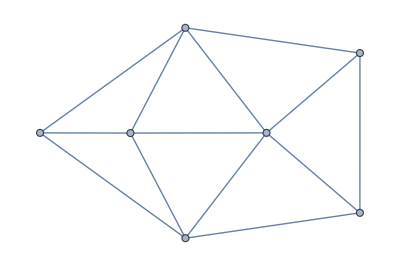

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->6,3<->6,4<->6,5<->6,7<->6,7<->2,7<->5,7<->1}]
```

Part::partw: Part 7 of {{1, 3}, {2, 6}, {4}, {5}, {7}} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 7 of {{1, 3}, {2}, {4}, {5}, {6}, {7}} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partw: Part 7 of {{1, 4}, {2, 6}, {3}, {5}, {7}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

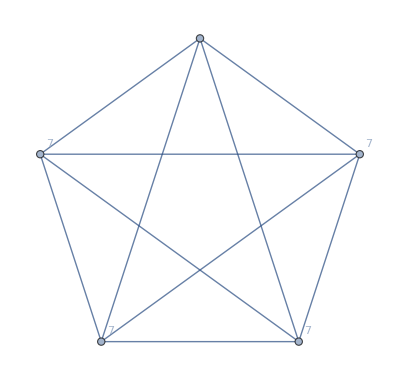
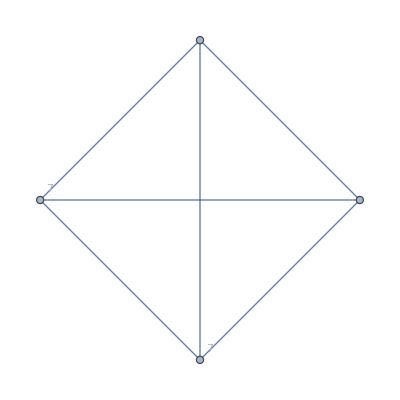
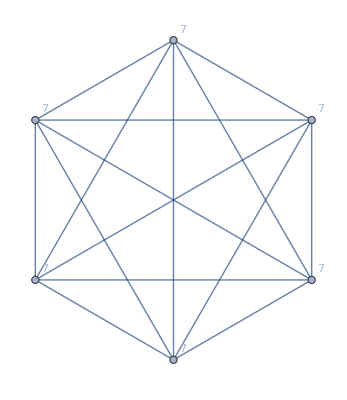
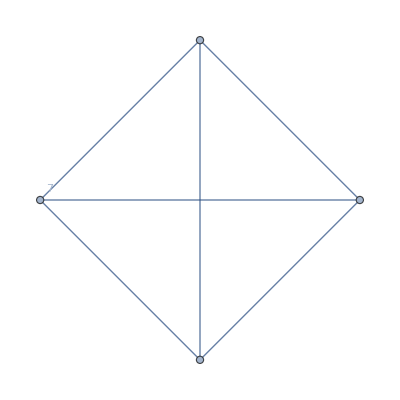
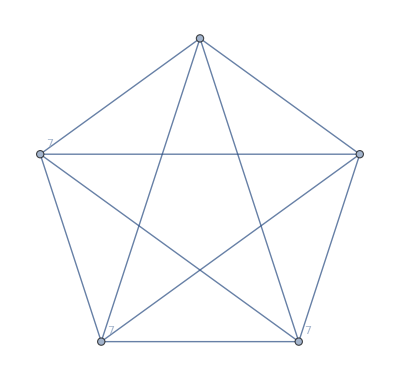
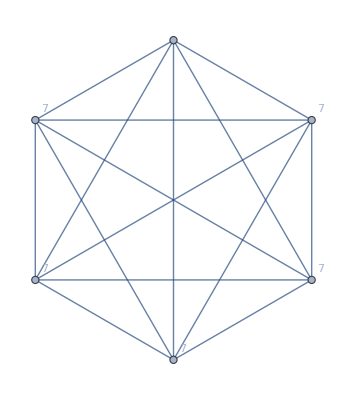
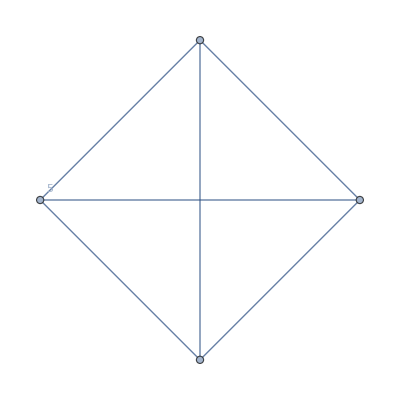
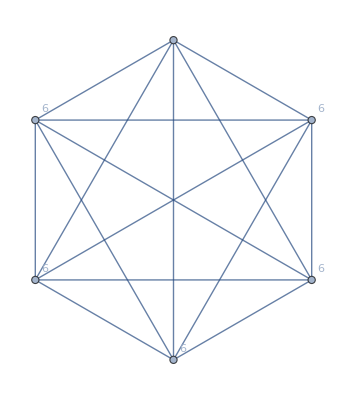
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ComputeGraph[Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,2<->6,3<->6,4<->6,5<->6,7<->6,7<->2,7<->5,7<->1}],Table[{k},{k,7}]]
```